Rechnung zu einer einzelnen Windung der Phase

Rechnung für konstante und kosinusförmige effektive Geschwindigkeit

```mathematica
σx=τx=PauliMatrix[1];
σy=τy=PauliMatrix[2];
σz=τz=PauliMatrix[3];
σ0=τ0=IdentityMatrix[2];
σ0τ0=KroneckerProduct[τ0,σ0];
σxτz=KroneckerProduct[τz,σx];
σyτz=KroneckerProduct[τz,σy];
σxτy=KroneckerProduct[τy,σx];
σyτy=KroneckerProduct[τy,σy];
σzτy=KroneckerProduct[τy,σz];
τx11=KroneckerProduct[τx,σ0];
τy11=KroneckerProduct[τy,σ0];
τz11=KroneckerProduct[τz,σ0];
σz11=KroneckerProduct[τ0,σz];
```

1 Windung der Phase, v = const. , ϵ = ϵ0 cos(π/2m)

```mathematica
(*Parameter definieren*)
Ntrunc=400;    (*Trunkierung:n von-Ntrunc bis Ntrunc*)
m=1;

dim=2*Ntrunc+1;
M=ConstantArray[0,{dim,dim}];

Do[n=k-Ntrunc-1;
(*Diagonalelement:-v*n*(-1)^n*)
M[[k,k]]=-v*n/2*(-1)^n;
(*Off-Diagonale:a_{n+m} *)
indexPlus=k+m;
If[1<=indexPlus<=dim,M[[k,indexPlus]]=ϵ0/2];
(*Off-Diagonale:a_{n-m}*)
indexMinus=k-m;
If[1<=indexMinus<=dim,M[[k,indexMinus]]=ϵ0/2  ],
{k,1,dim}];

Print["Matrix M erstellt. Dimension: ",dim,"x",dim];
MatrixForm[M];
```

Matrix M erstellt. Dimension: 801x801

```mathematica
ϵ0Values={0.1,1,2};
vValues={0.00001,0.001,0.1,0.9};

valsUvecs={};

PlotTable={};
For[i=1,i<=Length[ϵ0Values],i++,
sysPart={};
plotPart={};
For[j=1,j<=Length[vValues],j++,
{vals,vecs}=Eigensystem[M/. {ϵ0->ϵ0Values[[i]],v->vValues[[j]]}];
AppendTo[sysPart,{vals,vecs}];
plot=ListPlot[Sort[vals][[380;;420]],AxesLabel->{"Index j","E"},PlotLabel->"Sortierte Eigenenergien E bei ϵ_1="<>ToString[ϵ0Values[[i]]]<>", v_eff="<> ToString[vValues[[j]]]];
(*Print["Plot "<>i<>j<>" completed."];*)
AppendTo[plotPart,plot]
];
AppendTo[valsUvecs,sysPart];
AppendTo[PlotTable,plotPart];
]
```

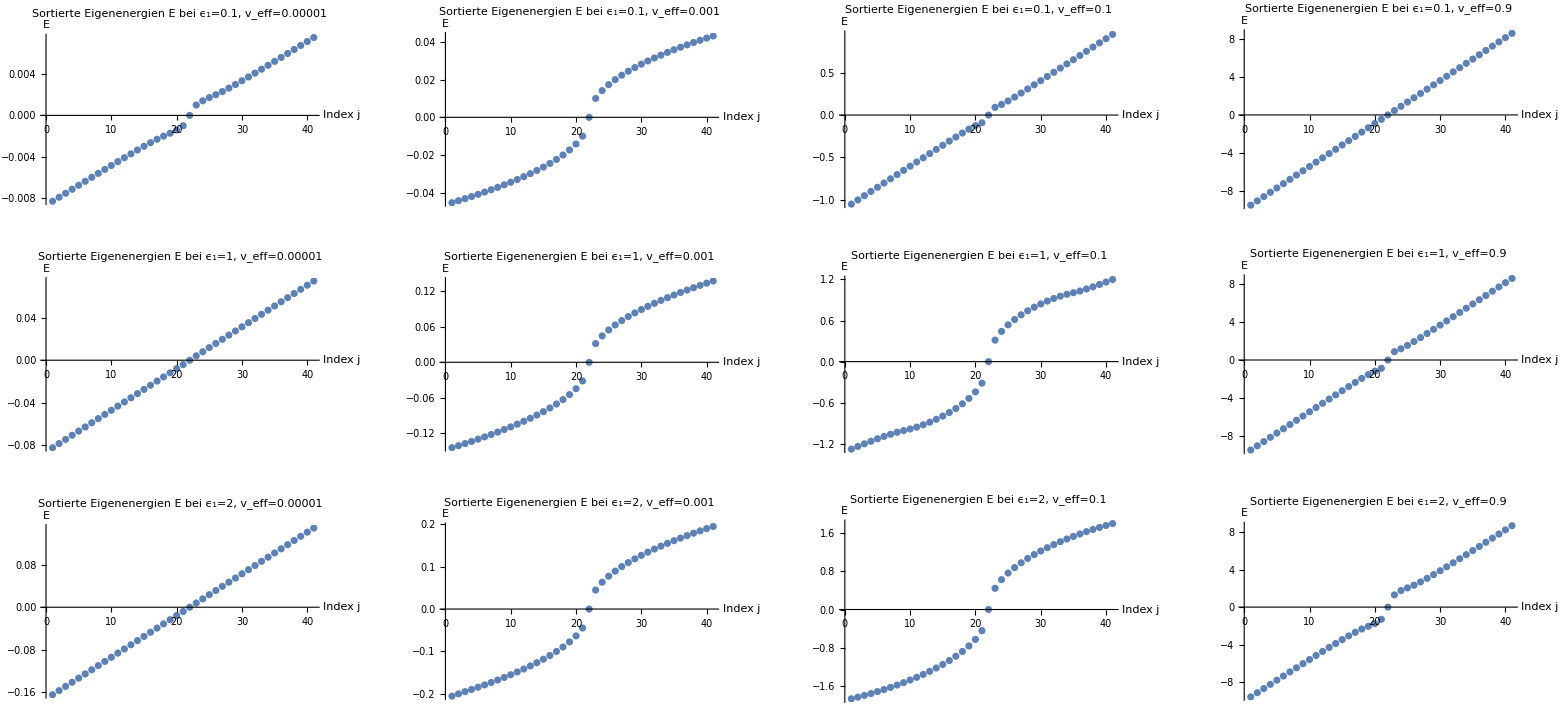

```mathematica
GraphicsGrid[PlotTable,ImageSize->Full]
```

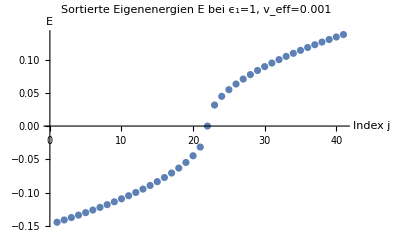

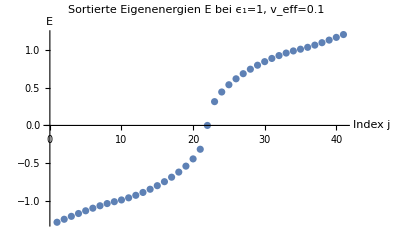

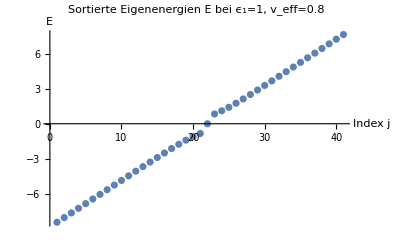

```mathematica
ϵ0Values={1};
vValues={0.001,0.1,0.8};

valsUvecs={};

PlotTable={};
For[i=1,i<=Length[ϵ0Values],i++,
sysPart={};
plotPart={};
For[j=1,j<=Length[vValues],j++,
{vals,vecs}=Eigensystem[M/. {ϵ0->ϵ0Values[[i]],v->vValues[[j]]}];
AppendTo[sysPart,{vals,vecs}];
plot=ListPlot[Sort[vals][[380;;420]],AxesLabel->{"Index j","E"},PlotLabel->"Sortierte Eigenenergien E bei ϵ_1="<>ToString[ϵ0Values[[i]]]<>", v_eff="<> ToString[vValues[[j]]]];
(*Print["Plot "<>i<>j<>" completed."];*)
AppendTo[plotPart,plot];
Print[plot]
];
AppendTo[valsUvecs,sysPart];
AppendTo[PlotTable,plotPart];
]
(*GraphicsRow[Flatten[PlotTable],ImageSize->Full]*)
```

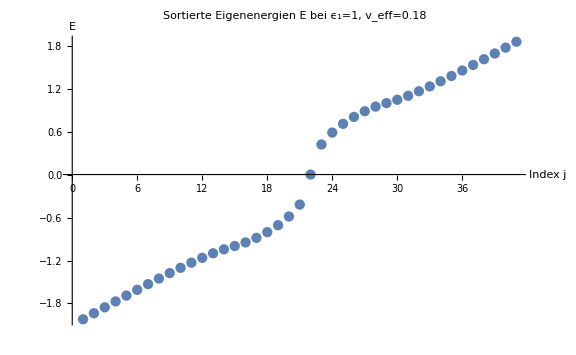

```mathematica
ϵTestSingle=1;
vTestSingle=0.18;
{NeigvalsSingle0,NeigvecsSingle0}=Eigensystem[M/.{ϵ0->ϵTestSingle,v->vTestSingle}];
ListPlot[Sort[NeigvalsSingle0][[380;;420]],
PlotLabel->"Sortierte Eigenenergien E bei ϵ_1="<>ToString[ϵTestSingle]<>", v_eff="<> ToString[vTestSingle],AxesLabel->{"Index j","E"},ImageSize->Large]
```

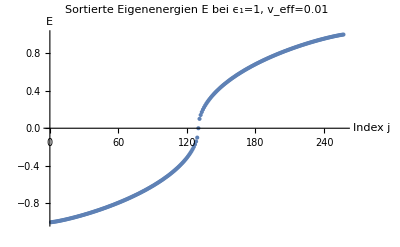

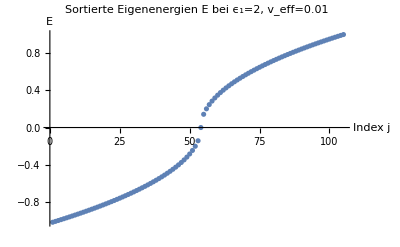

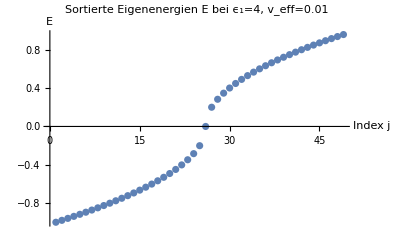

```mathematica
ϵTestSingle=1;
vTestSingle=0.01;
{NeigvalsSingle1,NeigvecsSingle1}=Eigensystem[M/.{ϵ0->ϵTestSingle,v->vTestSingle}];
plotSingle01=ListPlot[Sort[NeigvalsSingle1][[272;;528]],
PlotLabel->"Sortierte Eigenenergien E bei ϵ_1="<>ToString[ϵTestSingle]<>", v_eff="<> ToString[vTestSingle],AxesLabel->{"Index j","E"}];(*[[380;;420]]*)


ϵTestSingle=2;
vTestSingle=0.01;
{NeigvalsSingle1,NeigvecsSingle1}=Eigensystem[M/.{ϵ0->ϵTestSingle,v->vTestSingle}];
plotSingle02=ListPlot[Sort[NeigvalsSingle1][[348;;452]],
PlotLabel->"Sortierte Eigenenergien E bei ϵ_1="<>ToString[ϵTestSingle]<>", v_eff="<> ToString[vTestSingle],AxesLabel->{"Index j","E"}];


ϵTestSingle=4;
vTestSingle=0.01;
{NeigvalsSingle1,NeigvecsSingle1}=Eigensystem[M/.{ϵ0->ϵTestSingle,v->vTestSingle}];
plotSingle03=ListPlot[Sort[NeigvalsSingle1][[376;;424]],
PlotLabel->"Sortierte Eigenenergien E bei ϵ_1="<>ToString[ϵTestSingle]<>", v_eff="<> ToString[vTestSingle],AxesLabel->{"Index j","E"}];
(*GraphicsRow[{plotSingle01,plotSingle02,plotSingle03},ImageSize->Full]*)
Print[plotSingle01]
Print[plotSingle02]
Print[plotSingle03]
```

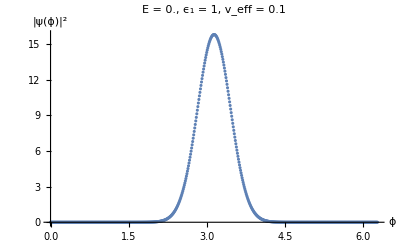

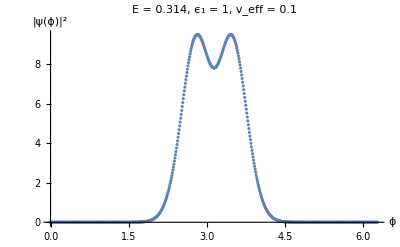

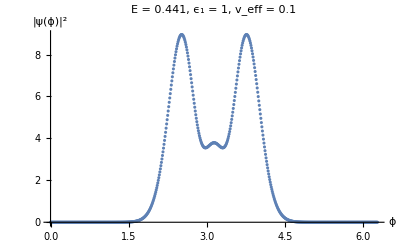

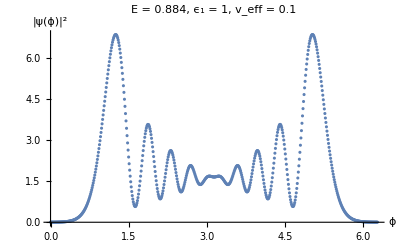

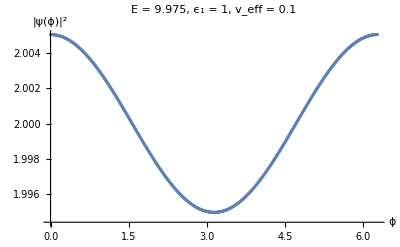

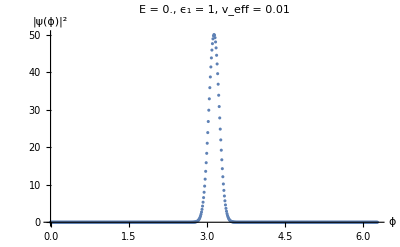

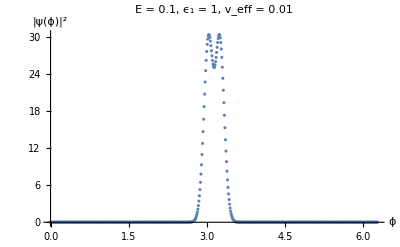

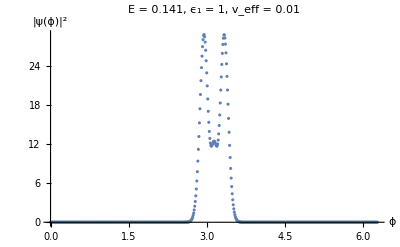

```mathematica
ϵTests={1,1,0.1};
vTests={0.1,0.01,0.1};
positions={401,402,403,410,600};

PsiPlots={};
For[j=1,j<=Length[vTests],j++,
{NeigvalsSingle1,NeigvecsSingle1}=Eigensystem[M/.{ϵ0->ϵTests[[j]],v->vTests[[j]]}];
{sortedNeigvalsSingle,sortedNeigvecsSingle}=Transpose[SortBy[Transpose[{NeigvalsSingle1,NeigvecsSingle1}],First]];
PsiPlotsRow={};
For[i=1,i<=Length[positions],i++,
pos=positions[[i]];
nValues=Range[-Ntrunc,Ntrunc];
vector1=E^(I*nValues/2 ϕ) ;
vector2=-E^(I*Pi*nValues) ;
ψ1=Total[sortedNeigvecsSingle[[pos]]*vector1];
ψ2=Total[sortedNeigvecsSingle[[pos]]*vector1*vector2];
ψ=Conjugate[{ψ1,ψ2}].{ψ1,ψ2};
PsiPlot=ListPlot[
Table[{ϕ,Re[ψ]},{ϕ,0,2Pi,0.01}],

PlotRange->All,AxesLabel->{"ϕ","|ψ(ϕ)|^2"},PlotLabel->"E = "<>ToString[Round[sortedNeigvalsSingle[[pos]],0.001]]<>", ϵ_1 = "<>ToString[ϵTests[[j]]]<>", v_eff = "<>ToString[vTests[[j]]]];
AppendTo[PsiPlotsRow,PsiPlot]
Print[PsiPlot]
];
AppendTo[PsiPlots,PsiPlotsRow];
(*Print[GraphicsRow[PsiPlotsRow,ImageSize->Full]]*)
]
```

1 Windung der Phase, v = v0 + v1 cos(π/2mv)  , ϵ = ϵ0 cos(π/2mϵ)

```mathematica
(*Parameter definieren*)
Ntrunc=400;    (*Trunkierung:n von-Ntrunc bis Ntrunc*)
l=1; (*ϵ - Terme*)

m=2;



dim=2*Ntrunc+1;
Mv=ConstantArray[0,{dim,dim}];

Do[n=k-Ntrunc-1;
(*Diagonalelement:a_{n}*)
Mv[[k,k]]=-v0*n/2*(-1)^n;
(*Off-Diagonale:a_{n+l} *)
indexPlusL=k+l;
If[1<=indexPlusL<=dim,Mv[[k,indexPlusL]]=ϵ0/2];
(*Off-Diagonale:a_{n-l}*)
indexMinusL=k-l;
If[1<=indexMinusL<=dim,Mv[[k,indexMinusL]]=ϵ0/2  ];



(*Off-Diagonale:a_{n+m} *)
indexPlusM=k+m;
If[1<=indexPlusM<=dim,Mv[[k,indexPlusM]]=-1/4 (-1)^(n+m) (n+m+m/2) v1];
(*Off-Diagonale:a_{n-m} *)
indexMinusM=k-m;
If[1<=indexMinusM<=dim,Mv[[k,indexMinusM]]=-1/4 (-1)^(n-m) (n-m-m/2) v1],
{k,1,dim}

]


Print["Matrix M erstellt. Dimension: ",dim,"x",dim];
MatrixForm[Mv];
```

Matrix M erstellt. Dimension: 801x801

```mathematica
ϵ0Values={1,1,1,1,1,1,1};
v0Values={0.9,0.5,0.1,0.01,0.001,0.0001,0.00001};
v1Values={0.3,0.2,0.05,0.01,0.001,0.0001,0.00001};

valsUvecs={};

ϵ0Value=1;
PlotTablev={};
For[i=1,i<=Length[ϵ0Values],i++,
sysPart={};
plotPart={};
For[j=1,j<=Length[v0Values],j++,
{vals,vecs}=Eigensystem[Mv/. {ϵ0->ϵ0Value,v0->v0Values[[i]],v1->v1Values[[j]]}];
AppendTo[sysPart,{vals,vecs}];
plot=ListPlot[Sort[vals][[380;;420]],PlotLabel->"ϵ_1="<>ToString[ϵ0Value]<>", v_0="<> ToString[v0Values[[i]]]<>", v_2="<> ToString[v1Values[[j]]],AxesLabel->{"Index j","E"}];
(*Print["Plot "<>i<>j<>" completed."];*)
AppendTo[plotPart,plot];
];
AppendTo[valsUvecs,sysPart];
AppendTo[PlotTablev,plotPart];
]
```

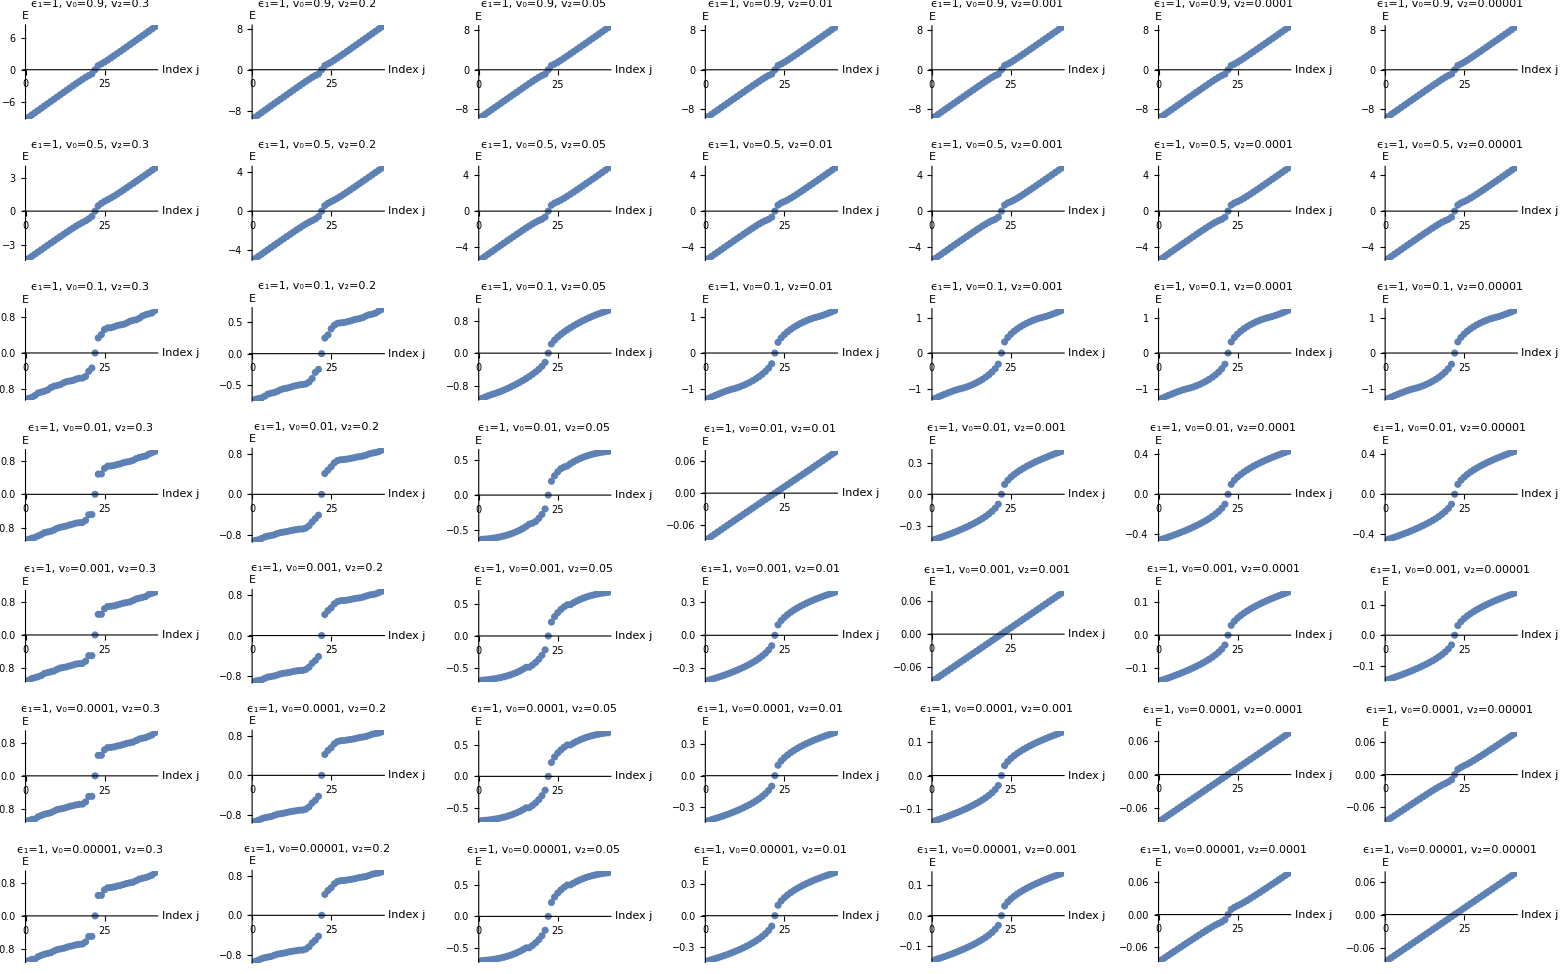

```mathematica
GraphicsGrid[PlotTablev,ImageSize->Full](*nicht alle Diagramme sind physikalisch sinnvoll; z.B. Subscript[v, 2]>Subscript[v, 0]*)
```

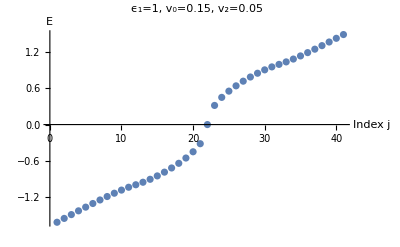

```mathematica
ϵ0TestSingle=1;
v0TestSingle=0.15;
v1TestSingle=0.05;
{NeigvalsSingle,NeigvecsSingle}=Eigensystem[Mv/.{ϵ0->ϵ0TestSingle,v0->v0TestSingle,v1->v1TestSingle}];
ListPlot[Sort[NeigvalsSingle][[380;;420]],
PlotLabel->"ϵ_1="<>ToString[ϵ0TestSingle]<>", v_0="<> ToString[v0TestSingle]<>", v_2="<> ToString[v1TestSingle],AxesLabel->{"Index j","E"}]
```

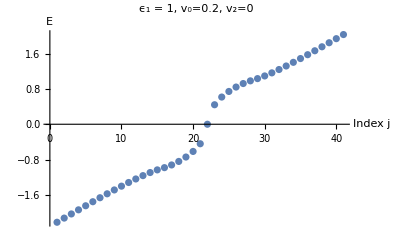

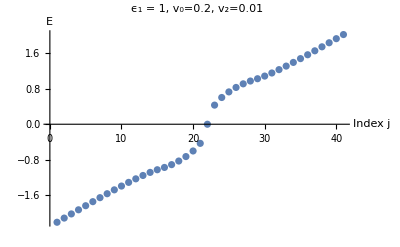

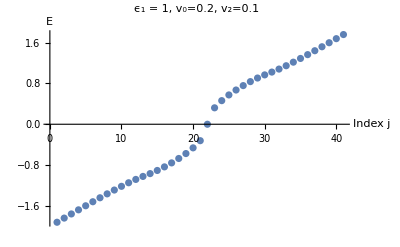

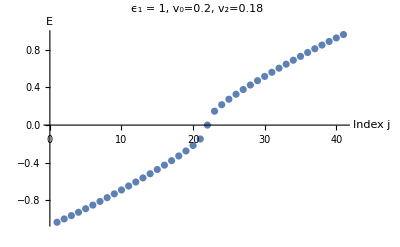

```mathematica
ϵ0TestSingle=1;
v0Tests={0.2};
v1Tests={0,0.01,0.1,0.18};

Plots={};
For[i=1,i<=Length[v1Tests],i++,
{NeigvalsSingle,NeigvecsSingle}=Eigensystem[Mv/.{ϵ0->ϵ0TestSingle,v0->v0Tests[[1]],v1->v1Tests[[i]]}];
plot=ListPlot[Sort[NeigvalsSingle][[380;;420]],
PlotLabel->"ϵ_1 = "<>ToString[ϵ0TestSingle]<>", v_0="<> ToString[v0Tests[[1]]]<>", v_2="<> ToString[v1Tests[[i]]],AxesLabel->{"Index j","E"}];
AppendTo[Plots,plot]
Print[plot]
]
(*GraphicsRow[Plots,ImageSize->Full]*)
```

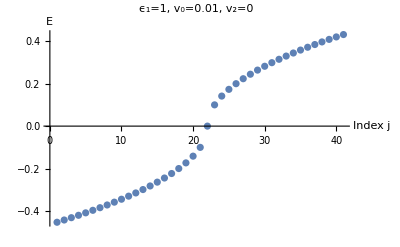

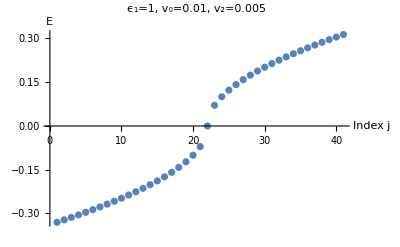

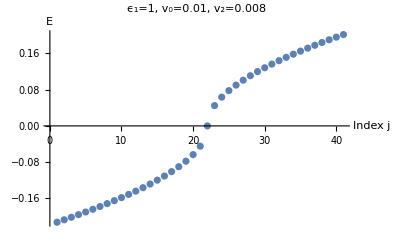

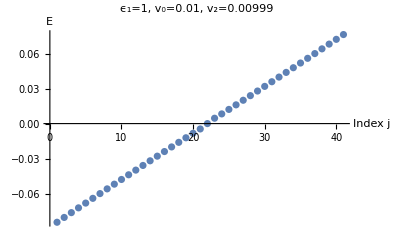

```mathematica
ϵ0TestSingle=1;
v0Tests={0.01};
v1Tests={0,0.005,0.008,0.00999};

Plots={};
For[i=1,i<=Length[v1Tests],i++,
{NeigvalsSingle,NeigvecsSingle}=Eigensystem[Mv/.{ϵ0->ϵ0TestSingle,v0->v0Tests[[1]],v1->v1Tests[[i]]}];
plot=ListPlot[Sort[NeigvalsSingle][[380;;420]],
PlotLabel->"ϵ_1="<>ToString[ϵ0TestSingle]<>", v_0="<> ToString[v0Tests[[1]]]<>", v_2="<> ToString[v1Tests[[i]]],AxesLabel->{"Index j","E"}];
AppendTo[Plots,plot]
Print[plot]
]
(*GraphicsRow[Plots,ImageSize->Full]*)
```

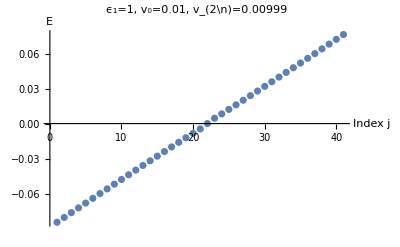

```mathematica
ϵ0TestSingle=1;
v0TestSingle=0.01;
v1TestSingle=0.00999;
{NeigvalsSingle,NeigvecsSingle}=Eigensystem[Mv/.{ϵ0->ϵ0TestSingle,v0->v0TestSingle,v1->v1TestSingle}];
ListPlot[Sort[NeigvalsSingle][[380;;420]],
PlotLabel->"ϵ_1="<>ToString[ϵ0TestSingle]<>", v_0="<> ToString[v0TestSingle]<>", v_(2\n)="<> ToString[v1TestSingle],AxesLabel->{"Index j","E"}]
```

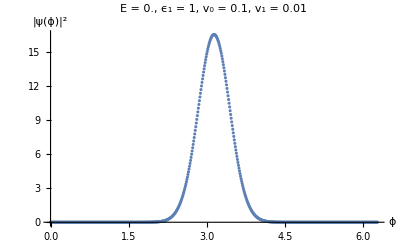

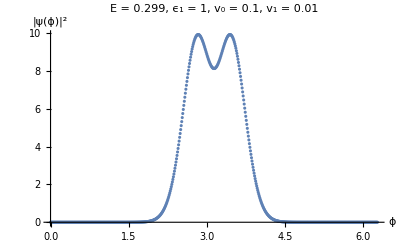

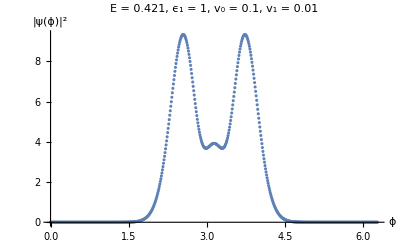

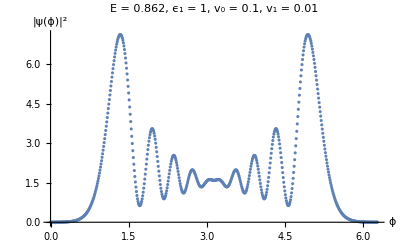

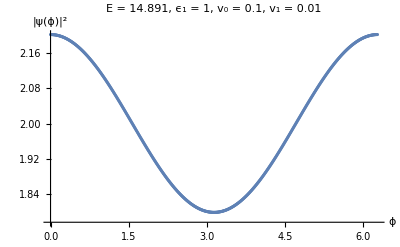

```mathematica
ϵTests={1};
v0Tests={0.1};
v1Tests={0.01};
positions={401,402,403,410,700};

PsiPlots={};
For[j=1,j<=Length[v1Tests],j++,
{NeigvalsSingle1,NeigvecsSingle1}=Eigensystem[Mv/.{ϵ0->ϵTests[[j]],v0->v0Tests[[j]],v1->v1Tests[[j]]}];
{sortedNeigvalsSingle,sortedNeigvecsSingle}=Transpose[SortBy[Transpose[{NeigvalsSingle1,NeigvecsSingle1}],First]];
PsiPlotsRow={};
For[i=1,i<=Length[positions],i++,
pos=positions[[i]];
nValues=Range[-Ntrunc,Ntrunc];
vector1=E^(I*nValues/2 ϕ) ;
vector2=-E^(I*Pi*nValues) ;
ψ1=Total[sortedNeigvecsSingle[[pos]]*vector1];
ψ2=Total[sortedNeigvecsSingle[[pos]]*vector1*vector2];
ψ=Conjugate[{ψ1,ψ2}].{ψ1,ψ2};
PsiPlot=ListPlot[
Table[{ϕ,Re[ψ]},{ϕ,0,2Pi,0.01}],

PlotRange->All,AxesLabel->{"ϕ","|ψ(ϕ)|^2"},PlotLabel->"E = "<>ToString[Round[sortedNeigvalsSingle[[pos]],0.001]]<>", ϵ_1 = "<>ToString[ϵTests[[j]]]<>", v_0 = "<>ToString[v0Tests[[j]]]<>", v_1 = "<>ToString[v1Tests[[j]]]];
AppendTo[PsiPlotsRow,PsiPlot];
Print[PsiPlot]
(*Print["Plot "<>j<>i<>" completed."]*)
];
AppendTo[PsiPlots,PsiPlotsRow]
]
(*GraphicsGrid[PsiPlots,ImageSize->Full]*)
```